# Trapped ions angular matrix elements calculation over Zeeman manifolds, for electric quadrupole transitions with its motional excitations as driven by spatially structured vector fields

This notebook is organized as follows:
- the propagating electric fields of interest are defined (the coordinate system is assumed to be with the z-direction along the light propagation direction and the x and y-axis along the transverse plane)
- the tensor field T^(2) , describing  quadrupole transitions with ΔJ=2,  is calculated for an angle θ_x, around the x-axis,  between  the light propagation direction and the magnetic quantization axis

Different quantities described in the paper are calculated:
- Fig1: electric field modulus components for different structured beams
- Fig2:  quadrupole (ΔJ=2) matrix element<J_f,m_f|T^(2)|J_i,m_i>  transverse cross sections for different dm_z transitions and different structured beams 
- Fig3: quadrupole (ΔJ=2) matrix element<J_f,m_f|T^(2)|J_i,m_i>  transverse cross sections for different θ_xangles and different structured beams
- Fig4: matrix element <J_f,m_f,n_(x,y,z)=1|T^(2)|J_i,m_i,n_(x,y,z)=0>  transverse cross sections for motional excitations (n_(x,y,z)=0 -> n_(x,y,z)=1) of quadrupole transitions (ΔJ=2)  for different structured beams

### Structured electric field of interest here (Laguerre-Gaussian and Hermite-Gaussian types):

- α = 1 :  HG(0,0) circularly polarized
- α = 2 :  HG(0,1) circularly polarized
- α = 3 :  LG(0,1) circularly polarized
- α = 4 :  LG(0,-1) circularly polarized
- α = 5 : LG(0,1) radially polarized
- α = 6 :  LG(0,1) azimuthally polarized

### Choose the structured electric field parameters

- P0 : power [W]
- w0 : waist [µm]
- p,l : beam parameters
- σ : polarization
- z0 : transverse plane of interest

```mathematica
P0=10^-3;    w0=1.0;      σ0=1;
z0=10^-3;    (* numerical infinites on the exact focal plane z=0 *)
```

### Defining the electric fields considered here: Hermite-Gaussian and Laguerre-Gaussian type

```mathematica
(* Physical constants *)
ϵ0=8.854187817 10^-18;     (* Subscript[ϵ, 0] [J/V^2 μm] *)   
c=2.99792458 10^14;           (* [μm/s] *)
ℏ=1.055 10^-34;                   (* [J*s] *)
λ=0.729;                             (* wavelenght [μm] *)
kz=2π/λ;                          (* wavevector [μm^-1] *)   
ω=c kz;                                (* 2πfrequency [Hz] *)

(* Optical functions *)
zR[w_]=π w^2/λ;                                             (* Rayleigh length *)
R[z_,w_]=z(1+(zR[w]/z)^2);                (* curvature radius *)
wz[z_,w_]=w √(1+(z/zR[w])^2);
El0[P_,w_]=√(4 P/(c ϵ0 w^2));           (* [V/μm] *)
ψ[z_,w_]=ArcTan[z/zR[w]];                 (* Gouy phase *)
ElHG[x_,y_,z_,p_,l_]=El0[P0,w0]/(√π) w0/wz[z,w0] HermiteH[p,(√2 x)/wz[z,w0]]HermiteH[l,(√2 y)/wz[z,w0]] ⅇ^(-(x^2+y^2)/wz[z,w0]^2)ⅇ^(I kz (x^2+y^2)/(2 R[z,w0]))ⅇ^(I ψ[z,w0])ⅇ^(I kz z);
ψLG[z_,p_,l_]=-(2p+Abs[l]+1) ArcTan[z/zR[w0]];      (* Generalized Gouy phase *)
ElLG[r_,ϕ_,z_,p_,l_]=El0[P0,w0]/(√2) √((2p!)/(π(p+Abs[l])!))w0/wz[z,w0]((r √2)/wz[z,w0])^Abs[l] ⅇ^(-r^2/wz[z,w0]^2)LaguerreL[p,Abs[l],(2 r^2)/wz[z,w0]^2] ⅇ^(I kz r^2/(2 R[z,w0]))ⅇ^(I l ϕ)ⅇ^(I ψLG[z,p,l])ⅇ^(I kz z);
```

### Electric fields considered here:

```mathematica
For[α=1,α<7,α++,{
Which[α==1,                                                                                            (* vector beam TEM(0,0) circularly polarized σ=+1 *)
u[x_,y_,z_,p_,l_]=ElHG[x,y,z,p,l];
ElField[x_,y_,z_][α,1]=u[x,y,z,0,0];
ElField[x_,y_,z_][α,2]=I σ0 u[x,y,z,0,0];
ElField[x_,y_,z_][α,3]=I/kz (D[u[x,y,z,0,0],x]+I σ0 D[u[x,y,z,0,0],y]);,

α==2,                                                                                            (* vector beam HG(0,1) circularly polarized σ=+1 *)
u[x_,y_,z_,p_,l_]=ElHG[x,y,z,p,l];
ElField[x_,y_,z_][α,1]=u[x,y,z,0,1];
ElField[x_,y_,z_][α,2]=I σ0 u[x,y,z,0,1];
ElField[x_,y_,z_][α,3]=I/kz (D[u[x,y,z,0,1],x]+I σ0  D[u[x,y,z,0,1],y]);,


α==3,                                                                                                      (* vector beam LG(0,1) circularly polarized σ=+1 *)
u[x_,y_,z_,p_,l_]=ElLG[√(x^2+y^2),ArcTan[x,y],z,p,l];  
ElField[x_,y_,z_][α,1]=u[x,y,z,0,1];
ElField[x_,y_,z_][α,2]=I σ0 u[x,y,z,0,1];
ElField[x_,y_,z_][α,3]=I/kz (D[u[x,y,z,0,1],x]+I σ0 D[u[x,y,z,0,1],y]);,

α==4,                                                                                                      (* vector beam LG(0,-1) circularly polarized σ=+1 *)
u[x_,y_,z_,p_,l_]=ElLG[√(x^2+y^2),ArcTan[x,y],z,p,l];  
ElField[x_,y_,z_][α,1]=u[x,y,z,0,-1];
ElField[x_,y_,z_][α,2]=I σ0 u[x,y,z,0,-1];
ElField[x_,y_,z_][α,3]=I/kz (D[u[x,y,z,0,-1],x]+I σ0 D[u[x,y,z,0,-1],y]);,

α==5,                                                                                                       (* vector beam LG(0,-1) radially polarized *)
u[x_,y_,z_,p_,l_]=1/(√2)ElLG[√(x^2+y^2),ArcTan[x,y],z,p,l];  
ElField[x_,y_,z_][α,1]=u[x,y,z,0,-1]+u[x,y,z,0,1];
ElField[x_,y_,z_][α,2]=I σ0  u[x,y,z,0,-1]-I σ0 u[x,y,z,0,1];
ElField[x_,y_,z_][α,3]=I/kz (D[u[x,y,z,0,-1],x]+D[u[x,y,z,0,1],x]+I σ0 D[u[x,y,z,0,-1],y]-I σ0 D[u[x,y,z,0,1],y]);,

α==6,                                                                                                   (* vector beam LG(p,l) azimuthally polarized *)
u[x_,y_,z_,p_,l_]=I/(√2)ElLG[√(x^2+y^2),ArcTan[x,y],z,p,l];   
ElField[x_,y_,z_][α,1]=u[x,y,z,0,-1]-u[x,y,z,0,1];
ElField[x_,y_,z_][α,2]=I σ0 u[x,y,z,0,-1]+I σ0 u[x,y,z,0,1];
ElField[x_,y_,z_][α,3]=I/kz (D[u[x,y,z,0,-1],x]-D[u[x,y,z,0,1],x]+I σ0 D[u[x,y,z,0,-1],y]+I σ0 D[u[x,y,z,0,1],y]);
];
}];
```

### General tensor T^(2) field driving quadrupole transitions (ΔJ=2)

```mathematica
WignerDl[j_,mm_,m_,θ_]:=Sum[(-1)^(k-m+mm)(√((j+m)!(j-m)!(j+mm)!(j-mm)!))/((j+m-k)!k!(j-k-mm)!(k-m+mm)!)Cos[θ/2]^(2j-2k+m-mm)Sin[θ/2]^(2k-m+mm),{k,Max[0,m-mm],Min[j+m,j-mm]}]    
Clear[TensorMatQ];
TensorMatQ[k_,q_,α_]=0;
(* Quadrupole Hamiltonian (restricted to ΔJ=2) in terms of the spherical tensor Subscript[T^2, q] with q=-2,-1,0,+1,+2 *)
For[α=1,α<7,α++,
Qm2[x_,y_,z_][α]=D[ElField[x,y,z][α,1],x] - D[ElField[x,y,z][α,2],y] +I D[ElField[x,y,z][α,2],x]+I D[ElField[x,y,z][α,1],y];
Qm1[x_,y_,z_][α]=D[ElField[x,y,z][α,3],x]+D[ElField[x,y,z][α,1],z]+I D[ElField[x,y,z][α,3],y]+I D[ElField[x,y,z][α,2],z];
Q0[x_,y_,z_][α]=2/√6(D[ElField[x,y,z][α,1],x] + D[ElField[x,y,z][α,2],y])+2 √(2/3)D[ElField[x,y,z][α,3],z];
Qp1[x_,y_,z_][α]=D[ElField[x,y,z][α,3],x]+D[ElField[x,y,z][α,1],z]-I D[ElField[x,y,z][α,3],y]-I D[ElField[x,y,z][α,2],z];
Qp2[x_,y_,z_][α]=D[ElField[x,y,z][α,1],x]-D[ElField[x,y,z][α,2],y]-I D[ElField[x,y,z][α,2],x]-I D[ElField[x,y,z][α,1],y];

TensorMatQ[2,-2,α]=Qm2[x,y,z][α];
TensorMatQ[2,-1,α]=Qm1[x,y,z][α];
TensorMatQ[2,0,α]=Q0[x,y,z][α];
TensorMatQ[2,1,α]=Qp1[x,y,z][α];
TensorMatQ[2,2,α]=Qp2[x,y,z][α];
ThetaTensorQ[k_,q_,α_]:=Sum[WignerDl[k,qq,q,θ]TensorMatQ[k,qq,α],{qq,-k,k}];
]
```

### Fig1: Electric field modulus components for different structured beams

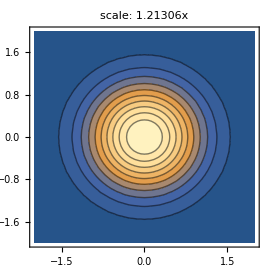
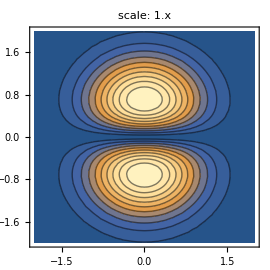
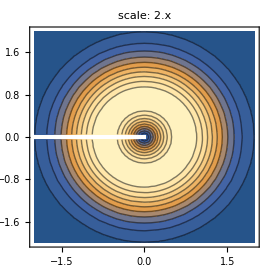
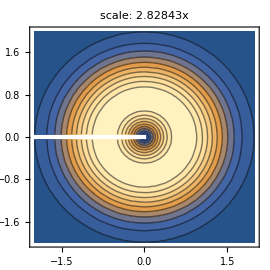
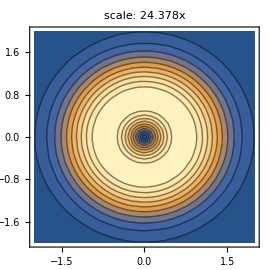
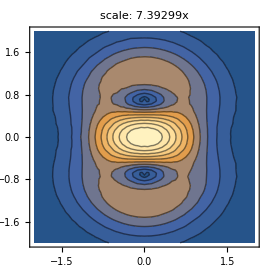
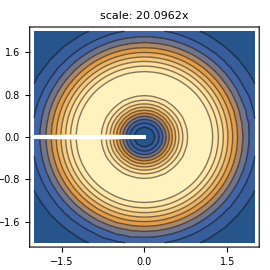
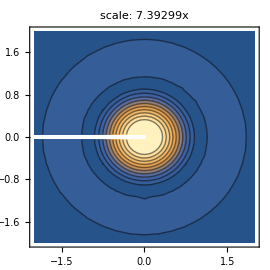
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
For[α=1,α<7,α++,
SqrtInt[x_,y_,z_][α,1]=Abs[ElField[x,y,z][α,1] -I ElField[x,y,z][α,2]];   (* |Subscript[E, σ=1]| *)
SqrtInt[x_,y_,z_][α,2]=Abs[ElField[x,y,z][α,3]];                                                          (* |Subscript[E, z]| *)
SqrtInt[x_,y_,z_][α,3]=Abs[ElField[x,y,z][α,1] +I ElField[x,y,z][α,2]];]   (* |Subscript[E, σ=-1]| *)
scale=ConstantArray[1,{6,3}];

For[α=1,α<7,α++,
For[n=1,n<4,n++,
ElMax[α,n]=FindMaximum[{SqrtInt[x,y,z0][α,n],{x,y}∈Disk[{x,y},2w0]},{{x,0.5},{y,0.5}}][[1]];    
If[ElMax[α,n]< 10^-5,ElMax[α,n]=10^-10;SqrtInt[x_,y_,z_][α,n]=0;scale[[α,n]]=0;];
]]

MaxAllEl=Max@Table[ElMax[αi,ni],{αi,1,6},{ni,1,3}];
numPoints=5;
Table[ContourPlot[1/ElMax[αi,ni] SqrtInt[x,y,z0][αi,ni],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints, LabelStyle->Directive[Black,25],PlotRange->All,Contours->10,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],ColorFunctionScaling->False,PlotLabel->Style[Text[ "scale: "<> ToString[MaxAllEl/ElMax[αi,ni]*scale[[αi,ni]]]<>"x"]1,15,Black]],{ni,1,3},{αi,1,6}]
```

### Fig2: quadrupole (ΔJ=2) matrix element cross sections for different dm_z transitions and different structured beams

- choose the initial and final Zeeman sub-levels: minQ and mfinQ

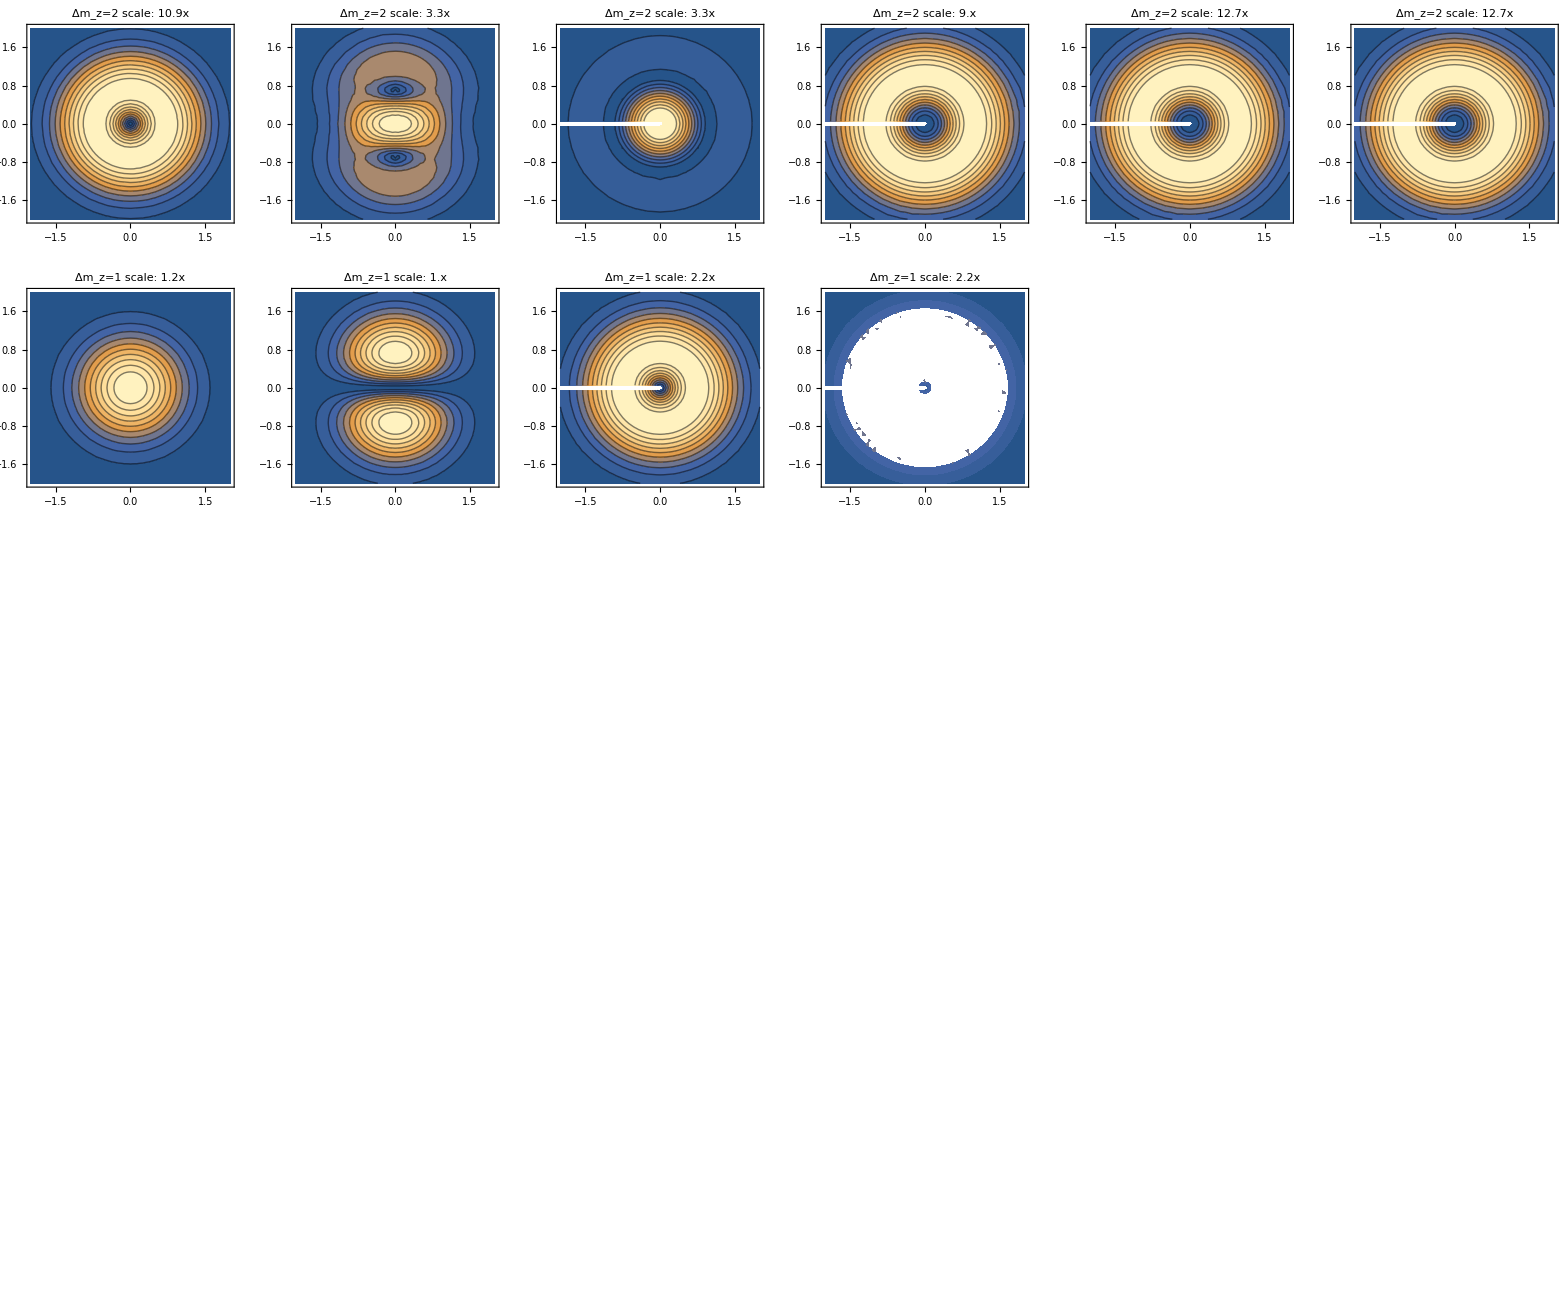

```mathematica
minQ=1/2;
mfinQ={5/2,3/2,1/2,-1/2,-3/2}; 
MaxAllEl=0;
scale=Table[0,{αi,1,6},{βi,1,Length@mfinQ}];
For[α=1,α<7,α++,
For[β=1,β<Length@mfinQ+1,β++,
Clear[θ];
dkQ=2;     (* quadrupole transitions restricted to ΔJ=2 *)
jinQ=1/2;
jfinQ=jinQ+dkQ;
μQ[mmQ_]=Sum[ThetaTensorQ[dkQ,q,α]ClebschGordan[{jinQ,minQ},{dkQ,q},{jfinQ,mmQ}],{q,-dkQ,dkQ}];
θ=N@{0};   (* [rad] *)
μQxy[x_,y_,z_]=μQ[mfinQ[[β]]][[1]];
MaxμQ=FindMaximum[{Abs@μQxy[x,y,z0],{x,y}∈Disk[{x,y},2w0]},{{x,w0/2},{y,-w0/2}}][[1]];
If[MaxμQ>MaxAllEl,MaxAllEl=MaxμQ];
If[MaxμQ> 10^-5,scale[[α,β]]=1/MaxμQ,scale[[α,β]]=0];]]

For[α=1,α<7,α++,
For[β=1,β<Length@mfinQ+1,β++,
Clear[θ];
μQ[mmQ_]=Sum[ThetaTensorQ[dkQ,q,α]ClebschGordan[{jinQ,minQ},{dkQ,q},{jfinQ,mmQ}],{q,-dkQ,dkQ}];
θ=N@{0};   (* [rad] *)
μQxy[x_,y_,z_]=μQ[mfinQ[[β]]][[1]];
numPoints=5;
p[α,β]=ContourPlot[scale[[α,β]]Abs@μQxy[x,y,z0],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints, LabelStyle->Directive[Black,15],PlotRange->All,LabelStyle->{Plain,Black,FontSize->14},Contours->10,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],ColorFunctionScaling->False,PlotLabel->Style[Text[ "Δm_z=" <>ToString[mfinQ[[β]]-minQ]<>"    scale: "<> ToString[Round[MaxAllEl scale[[α,β]],0.1]]<>"x"]1,13,Black]]
]]
GraphicsGrid[Table[p[αi,βi],{βi,1,Length@mfinQ},{αi,1,6}],ImageSize->1700]
```

### Fig3: quadrupole (ΔJ=2) matrix element cross sections for different θ_xangles and different structured beams

- choose the initial level (jin,min) and the final Zeeman sub-level (mfin)
- choose the different angles θ_x

```mathematica
minQ=1/2;
mfinQ={1/2}; 
dkQ=2;     (* quadrupole transitions restricted to ΔJ=2 *)
jinQ=1/2;
jfinQ=jinQ+dkQ;
θkB=N@{0,π/100,π/4,π/2};   (* [rad] *)
scale=Table[0,{αi,1,6},{βi,1,Length@θkB}];
For[α=1,α<7,α++,
For[β=1,β<Length@θkB+1,β++,
Clear[θ];
μQ[mmQ_]=Sum[ThetaTensorQ[dkQ,q,α]ClebschGordan[{jinQ,minQ},{dkQ,q},{jfinQ,mmQ}],{q,-dkQ,dkQ}];
θ=θkB[[β]];   (* [rad] *)
μQxy[x_,y_,z_]=μQ[mfinQ[[1]]];
MaxμQ=FindMaximum[{Abs@μQxy[x,y,z0],{x,y}∈Disk[{x,y},2w0]},{{x,w0/2},{y,-w0/2}}][[1]];
If[MaxμQ>MaxAllEl,MaxAllEl=MaxμQ];
If[MaxμQ> 10^-5,scale[[α,β]]=1/MaxμQ,scale[[α,β]]=0];
]]
For[α=1,α<7,α++,
For[β=1,β<Length@θkB+1,β++,
Clear[θ];
μQ[mmQ_]=Sum[ThetaTensorQ[dkQ,q,α]ClebschGordan[{jinQ,minQ},{dkQ,q},{jfinQ,mmQ}],{q,-dkQ,dkQ}];
θ=θkB[[β]];   (* [rad] *)
μQxy[x_,y_,z_]=μQ[mfinQ[[1]]];
numPoints=5;
p[α,β]=ContourPlot[scale[[α,β]]Abs@μQxy[x,y,z0],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints, LabelStyle->Directive[Black,15],PlotRange->All,LabelStyle->{Plain,Black,FontSize->14},Contours->10,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],ColorFunctionScaling->False,PlotLabel->Style[Text[ "Δm_z=" <>ToString[mfinQ[[1]]-minQ]<>"    scale: "<> ToString[Round[MaxAllEl scale[[α,β]],0.1]]<>"x"]1,13,Black]];
]]
GraphicsGrid[Table[p[αi,βi],{βi,1,Length@θkB},{αi,1,6}],ImageSize->1700]
```

-Graphics-

### Fig4: quadrupole (ΔJ=2) motional excitations matrix element cross sections for one particular dm_z transitions and θ_x angle

- choose the transition: initial level (jin,min) and the final Zeeman level mfin
- choose the angle θ_x

```mathematica
jinQ=1/2;       minQ=1/2;          mfinQ=3/2;            θkB=N@{0};   (* [rad] *)
Clear[θ]
Clear[MaxμQ]
dkQ=2;     (* quadrupole transitions restricted to ΔJ=2 *)

jfinQ=jinQ+dkQ;
μQ[mmQ_]=Table[Sum[ThetaTensorQ[dkQ,q,αi]ClebschGordan[{jinQ,minQ},{dkQ,q},{jfinQ,mmQ}],{q,-dkQ,dkQ}],{αi,1,6}];
θ=θkB;   (* [rad] *)
μQ[mfinQ][[6,1]];
μQxy[x_,y_,z_]=Table[μQ[mfinQ][[αi,1]],{αi,1,6}];

scale=ConstantArray[1,{6,4}];
MaxAll=0;

For[α=1,α<7,α++,
MaxμQ[α]=FindMaximum[{Abs@μQxy[x,y,z0][[α]],{x,y}∈Disk[{x,y},2w0]},{{x,w0/2},{y,w0/4}}][[1]];    
If[MaxμQ[α]> MaxAll,MaxAll=MaxμQ[α];];
If[MaxμQ[α]< 10^-5,scale[[α,1]]=0;];
]

(* trap parameters *)
mCa=40 1.66 10^-27;    (* 40 Ca^+ approx mass [kg] *)
ωX=2π 1 10^6;                  (* [Hz] *)
ωY=2π 1 10^6;                 (* [Hz] *)
ωZ=2π 1 10^6;                 (* [Hz] *)

For[α=1,α<7,α++,
μQMot[x_,y_,z_][α,1]=10^6 √(ℏ/(2 mCa ωX))D[μQxy[x,y,z][[α]],x];   
μQMot[x_,y_,z_][α,2]=10^6 √(ℏ/(2 mCa ωY))D[μQxy[x,y,z][[α]],y];                                                     
μQMot[x_,y_,z_][α,3]=10^6 √(ℏ/(2 mCa ωZ))D[μQxy[x,y,z][[α]],z];]   

For[α=1,α<7,α++,
For[n=1,n<4,n++,
MaxμQMot[α,n]=FindMaximum[{Abs@μQMot[x,y,z0][α,n],{x,y}∈Disk[{x,y},2w0]},{{x,0.1},{y,0.2}},AccuracyGoal->2,PrecisionGoal->2][[1]];    
If[MaxμQMot[α,n]< 10^-5,scale[[α,n+1]]=0;];
]]


numPoints=5;
Table[ContourPlot[Abs[scale[[αi,1]]/MaxμQ[αi] μQxy[x,y,z0][[αi]]],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints, LabelStyle->Directive[Black,15],PlotRange->All,Contours->10, ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],PlotLabel->Style[Text[ "Δm_z=" <>ToString[mfinQ-minQ]<>"    θ_x ="<>ToString[Round[θ[[1]],0.1]]<>"    scale: "<> ToString[Round[MaxμQ[1]/MaxμQ[αi],0.1]]<>"x"]1,15,Black]],{αi,1,6}]
Table[ContourPlot[Abs[scale[[αi,2]]/MaxμQMot[αi,1] μQMot[x,y,z0][αi,1]],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints,LabelStyle->Directive[Black,15],PlotRange->All,Contours->10,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],PlotLabel->Style[Text[ "    scale: ("<> ToString[Round[(MaxμQ[1](√2)/w0*10^6 √(ℏ/(2 mCa ωX)))/MaxμQMot[αi,1],0.1]]<>")η_x^-1 x"]1,15,Black]],{αi,1,6}]
Table[ContourPlot[Abs[scale[[αi,3]]/MaxμQMot[αi,2] μQMot[x,y,z0][αi,2]],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints,LabelStyle->Directive[Black,15],PlotRange->All,Contours->10,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],PlotLabel->Style[Text[ "    scale: ("<> ToString[Round[(MaxμQ[1](√2)/w0*10^6 √(ℏ/(2 mCa ωY)))/MaxμQMot[αi,2],0.1]]<>")η_y^-1 x"]1,15,Black]],{αi,1,6}]
Table[ContourPlot[Abs[scale[[αi,4]]/MaxμQMot[αi,3] μQMot[x,y,z0][αi,3]],{x,-2w0,2w0},{y,-2w0,2w0},ImageSize->270,PlotPoints->numPoints,LabelStyle->Directive[Black,15],PlotRange->All,Contours->10,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1}}],PlotLabel->Style[Text[ "    scale: ("<> ToString[Round[(MaxμQ[1]kz*10^6 √(ℏ/(2 mCa ωZ)))/MaxμQMot[αi,3],0.1]]<>")η_z^-1 x"]1,15,Black]],{αi,1,6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

«1 more identical outputs»